# Zapori v Evropki uniji

Datum : 23. 3. 2021

## Podatki, ki jih bomo uporabili:

```mathematica
steviloZapornikovEvropa = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\persons_held_total.xlsx", "Dataset",HeaderLines->1][[1]];
```

```mathematica
evropskeDrzaveZaporniki = Select[steviloZapornikovEvropa, #[[1]]=="Europe" && !MemberQ[#,""]&];
```

### ŽENSKE ZAPORNICE

```mathematica
Zenske = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\female_rel.xlsx",{"Dataset",4},HeaderLines->1]
```

```mathematica
Drzave = evropskeDrzaveZaporniki[All,"Country"]//Normal;
```

```mathematica
PraveDrzaveZenske = Select[Normal[Zenske[All,"COUNTRY"]], MemberQ[Drzave,#]&];
```

```mathematica
PopolniZenske2018=Select[Zenske,#[[11]]≠":"&&MemberQ[PraveDrzaveZenske,#[[1]]]&][All,{"COUNTRY","2018"}];
```

```mathematica
DSV2=PopolniZenske2018[All,List[If[#COUNTRY=="Czechia",Entity["Country","CzechRepublic"],Entity["Country",#COUNTRY]]-> #[[2]]]&];
```

```mathematica
GeoRegionValuePlot[DSV2//Normal//Flatten,PlotLabel->"Število žensk v zaporih leta 2018 na 100000"]
```

-Graphics-

V tem razdelku je na zemljevidu prikazana stopnja žensk v zaporih v posameznih državah v Evropi v letu 2018. Država z najvišjo stopnjo zaprtih žensk na 100000 prebivalcev je Češka Republika. Najmanjšo stopnja ima Danska. V zgornjem grafu so vključene države, ki so del tudi nadaljne analize.

```mathematica
ZenskeZapori2011=Select[Zenske,#[[4]]≠":"&][All,{"COUNTRY","2011"}]//Normal;
```

```mathematica
Kosovo=Entity["Country","Kosovo"];
```

```mathematica
DelezZenskUK = Select[ZenskeZapori2011,MemberQ[{"Northern Ireland (UK)","England and Wales","Scotland"},#COUNTRY]&];
```

```mathematica
UK = Entity["Country","UK"];
QuantityMagnitude[Entity["Country","Switzerland"][EntityProperty["Country","PovertyHeadcount",{"Date"->2018}]]]
```

14.6

```mathematica
NorthernIreland=Entity["AdministrativeDivision",{"NorthernIreland","UnitedKingdom"}];
```

```mathematica
Scotland=Entity["AdministrativeDivision",{"Scotland","UnitedKingdom"}];
```

```mathematica
Wales=Entity["AdministrativeDivision",{"Wales","UnitedKingdom"}];
```

```mathematica
England=Entity["AdministrativeDivision",{"England","UnitedKingdom"}];
```

```mathematica
vrednostUK[entiteta_]:=Last[Values[Select[DelezZenskUK,entiteta==#COUNTRY&]][[1]]];
```

```mathematica
CelotnoUK = ((vrednostUK["Scotland"]*(QuantityMagnitude[Scotland[EntityProperty["AdministrativeDivision","Population",{"Date"->2011}]]]/10^5))+(vrednostUK["Northern Ireland (UK)"]*(QuantityMagnitude[NorthernIreland[EntityProperty["AdministrativeDivision","Population",{"Date"->2011}]]]/10^5))+(vrednostUK["England and Wales"]*((QuantityMagnitude[Wales[EntityProperty["AdministrativeDivision","Population",{"Date"->2011}]]]+QuantityMagnitude[England[EntityProperty["AdministrativeDivision","Population",{"Date"->2011}]]])/10^5)))/(QuantityMagnitude[UK[EntityProperty["Country","Population",{"Date"->2011}]]]/10^5)
```

14.1673

```mathematica
Head[Normal[PositionIndex[ZenskeZapori2011]][[32]][[1]][[2]]]
```

Real

```mathematica
Nekaj = ZenskeZapori2011;
```

```mathematica
ZenskeZaporiBrezUK2011=Delete[ZenskeZapori2011,Values[Select[Normal[PositionIndex[Nekaj]],MemberQ[DelezZenskUK,#[[1]]]&]]];
```

```mathematica
DSV3=Dataset[ZenskeZaporiBrezUK2011][All,List[Which[#COUNTRY=="Czechia",Entity["Country","CzechRepublic"],#COUNTRY=="Germany (until 1990 former territory of the FRG)",Entity["Country","Germany"],#COUNTRY=="Kosovo (under United Nations Security Council Resolution 1244/99)",Entity["Country","Kosovo"],#COUNTRY=="Bosnia and Herzegovina",Entity["Country","Bosnia"],#COUNTRY=="North Macedonia",Entity["Country","Macedonia"],!MemberQ[{"Czechia","Germany (until 1990 former territory of the FRG)","Kosovo (under United Nations Security Council Resolution 1244/99)"},#COUNTRY],Entity["Country",#COUNTRY]]-> #[[2]]]&];
```

```mathematica
DSV3=Normal[DSV3];
```

```mathematica
DSV3=Append[DSV3,{UK->CelotnoUK}];
```

```mathematica
GeoRegionValuePlot[DSV3//Flatten,PlotLabel->"Število žensk v zaporih leta 2011 na 100000"]
```

-Graphics-

Če ta graf primerjamo s prejšnjim vidimo, da se je v primerjavi s pretklostjo stopnja zaprtih žensk znižala v večini držav.

### KAPACITETE

```mathematica
KapaciteteZaporov = Import["C:\\Users\\jrenc\\OneDrive\\Namizje\\ROM_projekt\\prison_capacity.xlsx",{"Dataset",4},HeaderLines->1];
```

```mathematica
KapacitetaSlovenija = KapaciteteZaporov[Select[#COUNTRY=="Slovenia"&]][All, Range[2,11]]//Normal//Values;
```

```mathematica
CasovnaVrstaKapacitetaSlovenija =TimeSeries[KapacitetaSlovenija,{Range[2009,2018]}]//Normal;
```

### PODATKI O ŠTEVILO ZAPORNIKOV V EVROPSKIH DRŽAVAH

### DRŽAVE ZAVZETE V ANALIZO PODATKOV

```mathematica
CzechRepublic = Entity["Country","CzechRepublic"];
```

```mathematica
Drzave1Enititete = List[CzechRepublic,England,Wales,Scotland];
```

```mathematica
Drzave2Entitete=Entity["Country",#]&/@Delete[Drzave,{{3},{15},{16}}];
```

```mathematica
DrzaveAnaliza=Join[Drzave2Entitete,Drzave1Enititete];
```

```mathematica
GeoListPlot[DrzaveAnaliza]
```

-Graphics-

Države in administrativne enote, ki so bila zavzete v analizo podatkov in pregledu gibanja števila zapornikov:

ŠTEVILO ZAPORNIKOV V SLOVENIJI 2003-2018

SLOVENIJA (ABSOLUTNE VREDNOSTI)

```mathematica
Slovenija = evropskeDrzaveZaporniki[Select[#Country=="Slovenia"&]];
```

```mathematica
SlovenijaRelativno = Slovenija[All, Join[{3},Range[6,36, 2]]][All,Range[2,17]]//Normal//Values;
```

```mathematica
SlovenijaRelativnoTimeSeries=TimeSeries[SlovenijaRelativno[[1]],{Range[2003,2018]}];
```

```mathematica
SlovenijaAbsolutno = Slovenija[All, Join[{3},Range[5,36, 2]]][All,Range[2,17]]//Normal//Values;
```

```mathematica
SlovenijaAbsolutnoTimeSeries=TimeSeries[SlovenijaAbsolutno[[1]],{Range[2003,2018]}];
```

```mathematica
SlovenijaAsolutnoTS0918=TimeSeries[SlovenijaAbsolutno[[1]][[7;;All]],{Range[2009,2018]}];
```

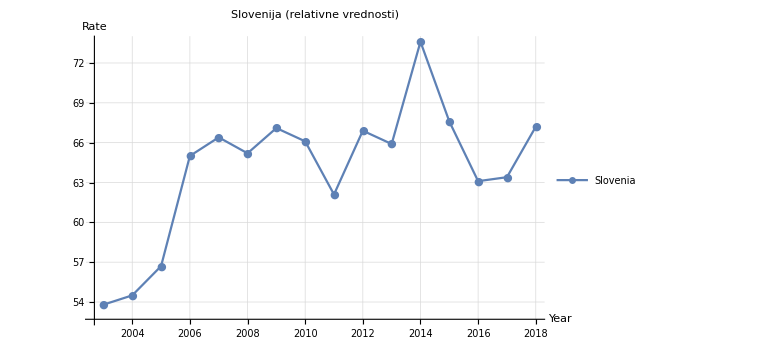

```mathematica
ListLinePlot[SlovenijaRelativnoTimeSeries,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->{"Slovenia"},PlotMarkers->{"●"},PlotLabel->Style["Slovenija (relativne vrednosti)",Large,Darker[Red]]]
```

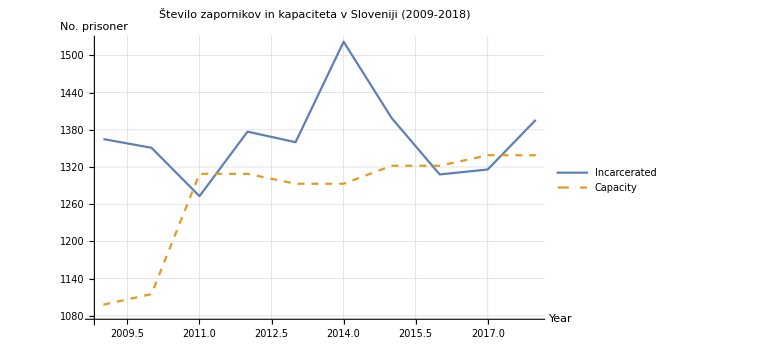

```mathematica
ListLinePlot[{SlovenijaAsolutnoTS0918,CasovnaVrstaKapacitetaSlovenija},AxesLabel->{"Year","No. prisoner"},PlotTheme->"Detailed",Frame->False,Axes->True,PlotLabel->Style["Število zapornikov in kapaciteta v Sloveniji (2009-2018)",Larger,Darker[Red]],PlotLegends->{"Incarcerated", "Capacity"},ImageSize->Large,PlotStyle->{Normal,Dashed}]
```

Število zapornikov je med leti 2011 in 2015 močno presegalo zmogljivosti slovenskih zaporov.

### PRIMERJAVA SLOVENIJA-ŠVEDSKA

```mathematica
Svedska=evropskeDrzaveZaporniki[Select[#Country=="Sweden"&]];
```

```mathematica
SvedskaRelativno = Svedska[All, Join[{3},Range[6,36, 2]]][All,Range[2,17]]//Normal//Values;
```

```mathematica
SvedskaRelativnoTimeSeries=TimeSeries[SvedskaRelativno[[1]],{Range[2003,2018]}];
```

```mathematica
SvedskaAbsolutno = Svedska[All, Join[{3},Range[5,36, 2]]][All,Range[2,17]]//Normal//Values;
```

```mathematica
SvedskaAbsolutnoTimeSeries=TimeSeries[SvedskaAbsolutno[[1]],{Range[2003,2018]}];
```

```mathematica
SvedskaAsolutnoTS0918=TimeSeries[SvedskaAbsolutno[[1]][[7;;All]],{Range[2009,2018]}];
```

```mathematica
KapacitetaSvedska = KapaciteteZaporov[Select[#COUNTRY=="Sweden"&]][All, Range[2,11]]//Normal//Values;
```

```mathematica
CasovnaVrstaKapacitetaSvedska =TimeSeries[KapacitetaSvedska,{Range[2009,2018]}]//Normal;
```

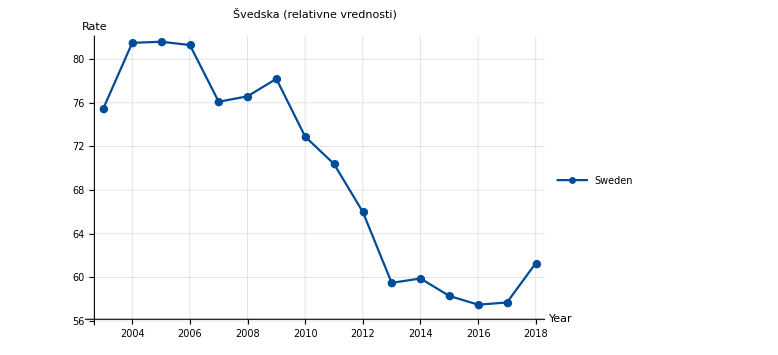

```mathematica
ListLinePlot[SvedskaRelativnoTimeSeries,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->{"Sweden"},PlotMarkers->{"●"},PlotLabel->Style["Švedska (relativne vrednosti)",Large,Darker[Red]],PlotStyle->RGBColor[0,76/255,153/255]]
```

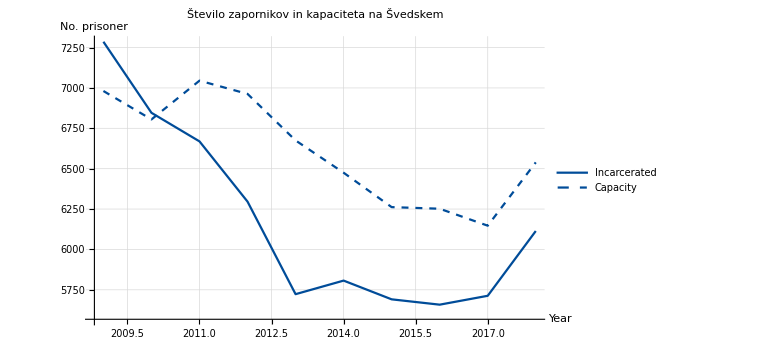

```mathematica
ListLinePlot[{SvedskaAsolutnoTS0918,CasovnaVrstaKapacitetaSvedska},AxesLabel->{"Year","No. prisoner"},PlotTheme->"Detailed",Frame->False,Axes->True,PlotLabel->Style["Število zapornikov in kapaciteta na Švedskem",Large,Darker[Red]],PlotLegends->{"Incarcerated", "Capacity"},ImageSize->Large,PlotStyle->{RGBColor[0,76/255,153/255],{Dashed,RGBColor[0,76/255,153/255]}}]
```

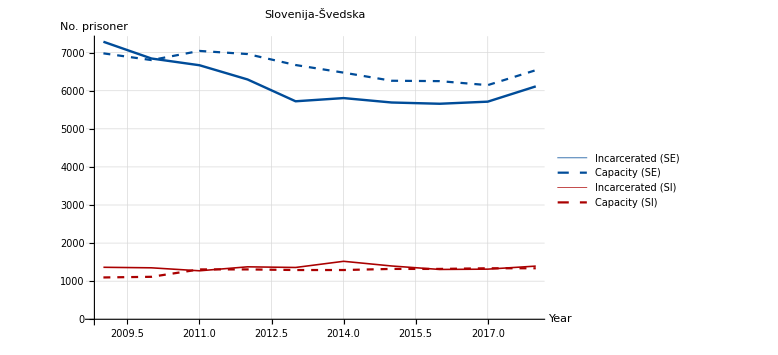

```mathematica
ListLinePlot[{SvedskaAsolutnoTS0918,CasovnaVrstaKapacitetaSvedska,SlovenijaAsolutnoTS0918,CasovnaVrstaKapacitetaSlovenija},AxesLabel->{"Year","No. prisoner"},PlotTheme->"Detailed",Frame->False,Axes->True,PlotLabel->Style["Slovenija-Švedska",Large,Darker[Red]],PlotLegends->{"Incarcerated (SE)", "Capacity (SE)","Incarcerated (SI)", "Capacity (SI)"},ImageSize->Large,PlotStyle->{{RGBColor[0,76/255,153/255],Thickness[0.003]},{Dashed, RGBColor[0,76/255,153/255]},{Darker[Red],Thickness[0.002]},{Dashed, Darker[Red]}}]
```

Na grafu je prikazano število zapornikov in kapacitete, ki jim lahko zapori zadostijo.

### PRIMERJAVA SLOVENIJA-MADŽARSKA

```mathematica
Madzarska=evropskeDrzaveZaporniki[Select[#Country=="Hungary"&]];
```

```mathematica
MadzarskaRelativno = Madzarska[All, Join[{3},Range[6,36, 2]]][All,Range[2,17]]//Normal//Values;
```

```mathematica
MadzarskaRelativnoTimeSeries=TimeSeries[MadzarskaRelativno[[1]],{Range[2003,2018]}];
```

```mathematica
MadzarskaAbsolutno = Madzarska[All, Join[{3},Range[5,36, 2]]][All,Range[2,17]]//Normal//Values;
```

```mathematica
MadzarskaAbsolutnoTimeSeries=TimeSeries[MadzarskaAbsolutno[[1]],{Range[2003,2018]}];
```

```mathematica
MadzarskaAsolutnoTS0918=TimeSeries[MadzarskaAbsolutno[[1]][[7;;All]],{Range[2009,2018]}];
```

```mathematica
KapacitetaMadzarska = KapaciteteZaporov[Select[#COUNTRY=="Hungary"&]][All, Range[2,11]]//Normal//Values;
```

```mathematica
CasovnaVrstaKapacitetaMadzarska =TimeSeries[KapacitetaMadzarska,{Range[2009,2018]}]//Normal;
```

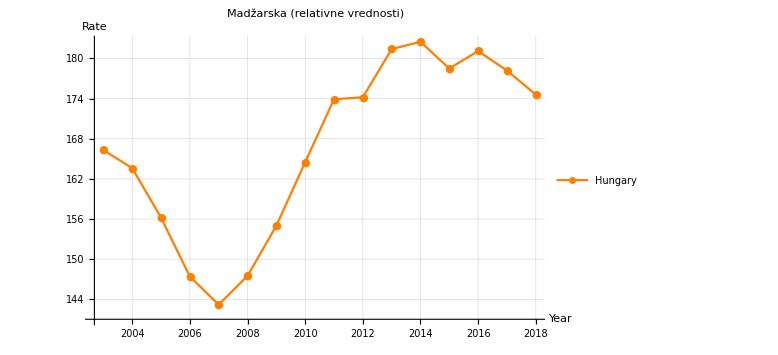

```mathematica
ListLinePlot[MadzarskaRelativnoTimeSeries,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->{"Hungary"},PlotMarkers->{"●"},PlotLabel->Style["Madžarska (relativne vrednosti)",Large,Darker[Red]],PlotStyle->RGBColor[1,128/255,0]]
```

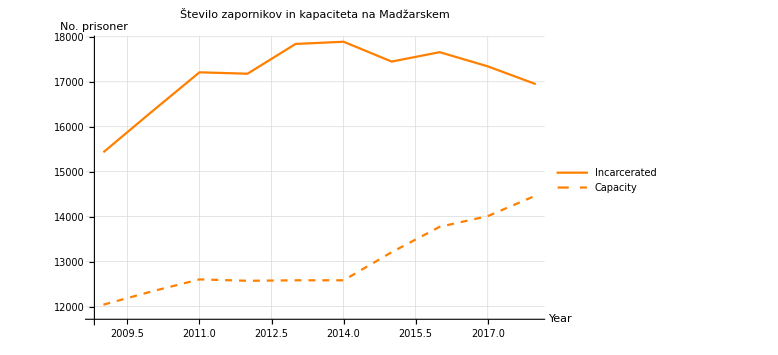

```mathematica
ListLinePlot[{MadzarskaAsolutnoTS0918,CasovnaVrstaKapacitetaMadzarska},AxesLabel->{"Year","No. prisoner"},PlotTheme->"Detailed",Frame->False,Axes->True,PlotLabel->Style["Število zapornikov in kapaciteta na Madžarskem",Large,Darker[Red]],PlotLegends->{"Incarcerated", "Capacity"},ImageSize->Large,PlotStyle->{{Normal,RGBColor[1,128/255,0]},{Dashed,RGBColor[1,128/255,0]}}]
```

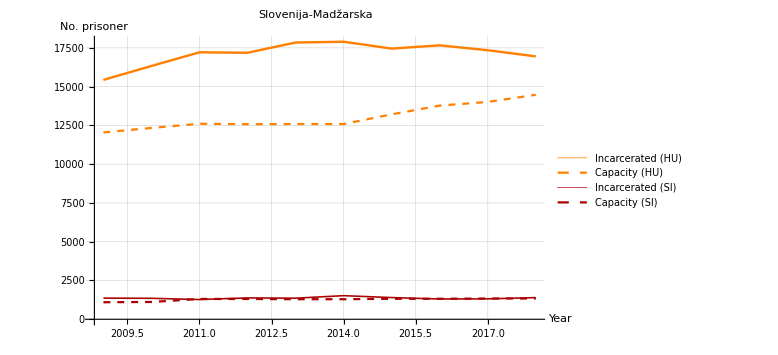

```mathematica
ListLinePlot[{MadzarskaAsolutnoTS0918,CasovnaVrstaKapacitetaMadzarska,SlovenijaAsolutnoTS0918,CasovnaVrstaKapacitetaSlovenija},AxesLabel->{"Year","No. prisoner"},PlotTheme->"Detailed",Frame->False,Axes->True,PlotLabel->Style["Slovenija-Madžarska",Large,Darker[Red]],PlotLegends->{"Incarcerated (HU)", "Capacity (HU)","Incarcerated (SI)", "Capacity (SI)"},ImageSize->Large,PlotStyle->{{RGBColor[1,128/255,0],Thickness[0.003]},{Dashed, RGBColor[1,128/255,0]},{Darker[Red],Thickness[0.002]},{Dashed, Darker[Red]}}]
```

### PRIMERJAVA SLOVENIJA-ITALIJA

```mathematica
Italija=evropskeDrzaveZaporniki[Select[#Country=="Italy"&]];
```

```mathematica
ItalijaRelativno = Madzarska[All, Join[{3},Range[6,36, 2]]][All,Range[2,17]]//Normal//Values;
```

```mathematica
ItalijaRelativnoTimeSeries=TimeSeries[ItalijaRelativno[[1]],{Range[2003,2018]}];
```

```mathematica
ItalijaAbsolutno = Italija[All, Join[{3},Range[5,36, 2]]][All,Range[2,17]]//Normal//Values;
```

```mathematica
ItalijaAbsolutnoTimeSeries=TimeSeries[ItalijaAbsolutno[[1]],{Range[2003,2018]}];
```

```mathematica
ItalijaAsolutnoTS0918=TimeSeries[ItalijaAbsolutno[[1]][[7;;All]],{Range[2009,2018]}];
```

```mathematica
KapacitetaItalija = KapaciteteZaporov[Select[#COUNTRY=="Italy"&]][All, Range[2,11]]//Normal//Values;
```

```mathematica
CasovnaVrstaKapacitetaItalija =TimeSeries[KapacitetaItalija,{Range[2009,2018]}]//Normal;
```

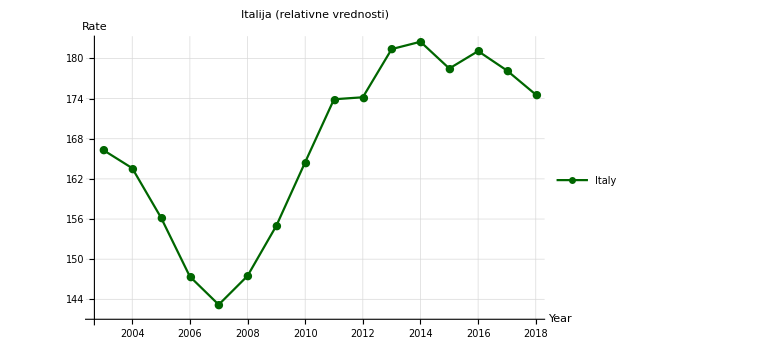

```mathematica
ListLinePlot[ItalijaRelativnoTimeSeries,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->{"Italy"},PlotMarkers->{"●"},PlotLabel->Style["Italija (relativne vrednosti)",Large,Darker[Red]],PlotStyle->RGBColor[0,102/255,0]]
```

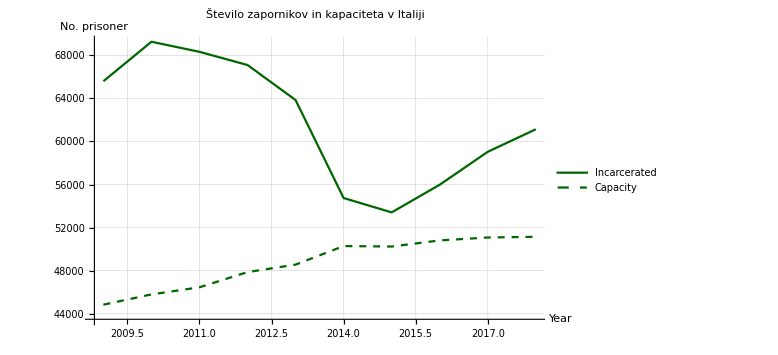

```mathematica
ListLinePlot[{ItalijaAsolutnoTS0918,CasovnaVrstaKapacitetaItalija},AxesLabel->{"Year","No. prisoner"},PlotTheme->"Detailed",Frame->False,Axes->True,PlotLabel->Style["Število zapornikov in kapaciteta v Italiji",Large,Darker[Red]],PlotLegends->{"Incarcerated", "Capacity"},ImageSize->Large,PlotStyle->{{Normal,RGBColor[0,102/255,0]},{Dashed,RGBColor[0,102/255,0]}}]
```

Kljub rasti števila zaprtih oseb se število kapacitet ni bistveno spremenilo.

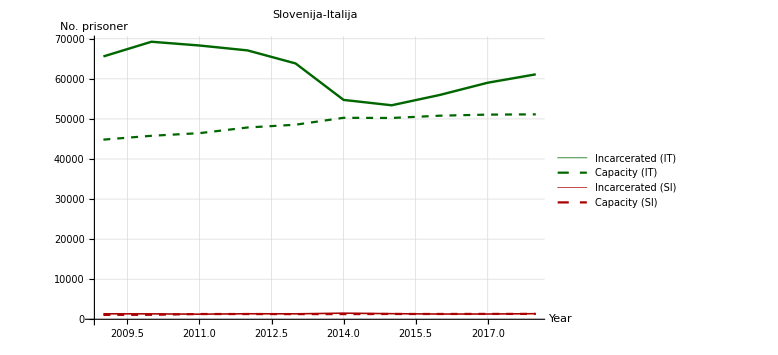

```mathematica
ListLinePlot[{ItalijaAsolutnoTS0918,CasovnaVrstaKapacitetaItalija,SlovenijaAsolutnoTS0918,CasovnaVrstaKapacitetaSlovenija},AxesLabel->{"Year","No. prisoner"},PlotTheme->"Detailed",Frame->False,Axes->True,PlotLabel->Style["Slovenija-Italija",Large,Darker[Red]],PlotLegends->{"Incarcerated (IT)", "Capacity (IT)","Incarcerated (SI)", "Capacity (SI)"},ImageSize->Large,PlotStyle->{{RGBColor[0,102/255,0],Thickness[0.003]},{Dashed, RGBColor[0,102/255,0]},{Darker[Red],Thickness[0.002]},{Dashed, Darker[Red]}},PlotRange->Full]
```

### ŠTEVILO ZAPRTIH JUŽNA EVROPA

```mathematica
DrzaveJuznaEvropa = evropskeDrzaveZaporniki[Select[#Subregion == "Southern Europe"&]][All, Join[{3},Range[6,36, 2]]];
```

```mathematica
VrednostiDrzaveJuznaEvropa =DrzaveJuznaEvropa[All, {Range[2,17]}]//Normal//Values;
```

```mathematica
CasovneVrsteDrzaveJuznaEvropa=TimeSeries[#,{Range[2003,2018]}]&/@VrednostiDrzaveJuznaEvropa;
```

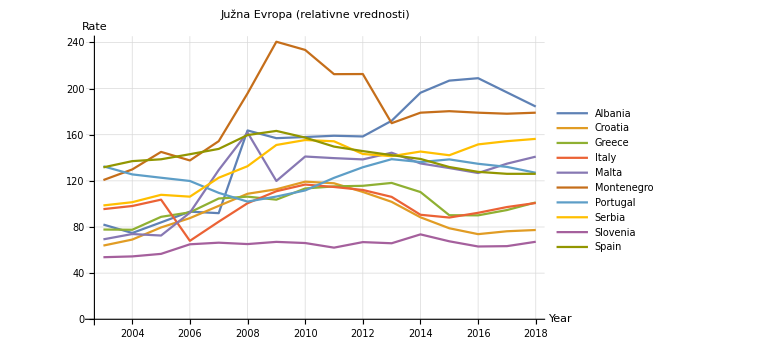

```mathematica
ListLinePlot[CasovneVrsteDrzaveJuznaEvropa,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->Normal[DrzaveJuznaEvropa[All, "Country"]],PlotLabel->Style["Južna Evropa (relativne vrednosti)",Large,Darker[Red]],PlotRange->Full]
```

Na zgornjem grafu je prikazano gibanje števila zapornikov med leti 2003 in 2018 v državah južne Evrope.

### ŠTEVILO ZAPRTIH VZHODNA EVROPA

```mathematica
DrzaveVzhodnaEvropa = evropskeDrzaveZaporniki[Select[#Subregion == "Eastern Europe"&]][All, Join[{3},Range[6,36, 2]]];
```

```mathematica
VrednostiDrzaveVzhodnaEvropa = DrzaveVzhodnaEvropa[All, Range[2,17]]//Normal//Values;
```

```mathematica
CasovneVrsteDrzaveVzhodnaEvropa=TimeSeries[#,{Range[2003,2018]}]&/@VrednostiDrzaveVzhodnaEvropa;
```

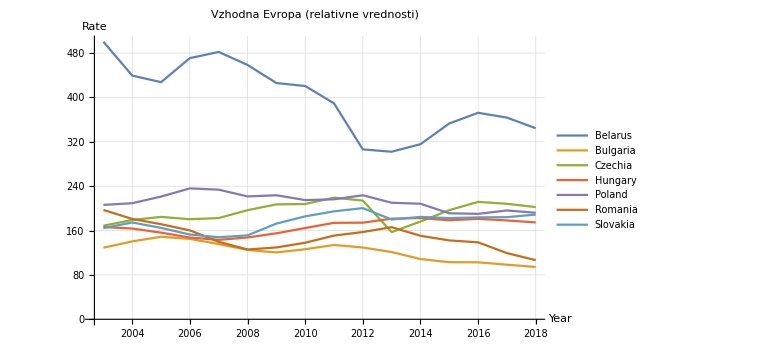

```mathematica
ListLinePlot[CasovneVrsteDrzaveVzhodnaEvropa,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->Normal[DrzaveVzhodnaEvropa[All, "Country"]],PlotLabel->Style["Vzhodna Evropa (relativne vrednosti)",Large,Darker[Red]],PlotRange->Full]
```

### ŠTEVILO ZAPRTIH SEVERNA EVROPA

```mathematica
DrzaveSevernaEvropa = evropskeDrzaveZaporniki[Select[#Subregion == "Northern Europe"&]][All, Join[{3},Range[6,36, 2]]];
```

```mathematica
VrednostiDrzaveSevernaEvropa = DrzaveSevernaEvropa[All, Range[2,17]]//Normal//Values;
```

```mathematica
CasovneVrsteDrzaveSevernaEvropa=TimeSeries[#,{Range[2003,2018]}]&/@VrednostiDrzaveSevernaEvropa;
```

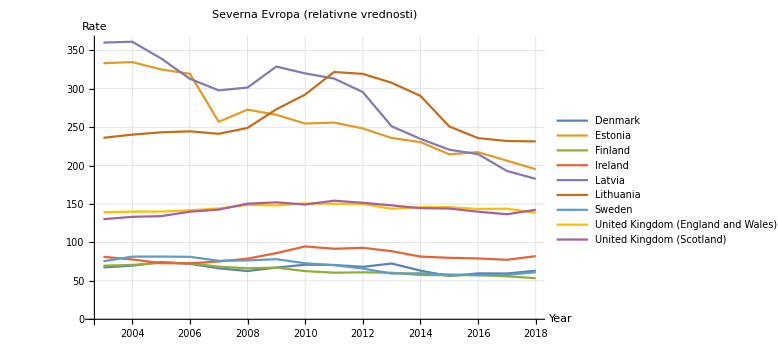

```mathematica
ListLinePlot[CasovneVrsteDrzaveSevernaEvropa,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->Normal[DrzaveSevernaEvropa[All, "Country"]],PlotLabel->Style["Severna Evropa (relativne vrednosti)",Large,Darker[Red]]]
```

### ŠTEVILO ZAPRTIH ZAHODNA EVROPA

```mathematica
DrzaveZahodnaEvropa = evropskeDrzaveZaporniki[Select[#Subregion == "Western Europe"&]][All, Join[{3},Range[6,36, 2]]];
VrednostiDrzaveZahodnaEvropa = DrzaveZahodnaEvropa[All, Range[2,17]]//Normal//Values;
```

```mathematica
CasovneVrsteDrzaveZahodnaEvropa=TimeSeries[#,{Range[2003,2018]}]&/@VrednostiDrzaveZahodnaEvropa;
```

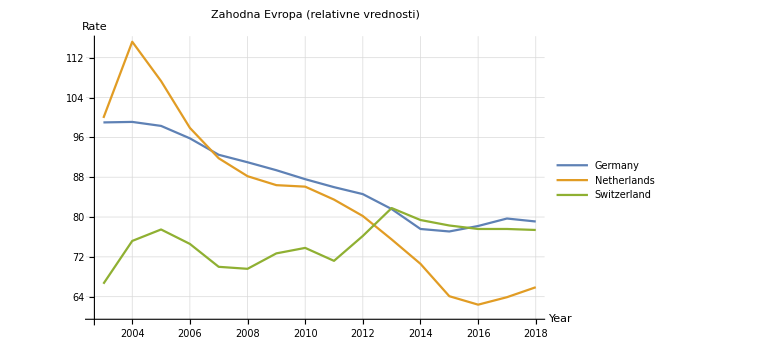

```mathematica
ListLinePlot[CasovneVrsteDrzaveZahodnaEvropa,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->Normal[DrzaveZahodnaEvropa[All, "Country"]],PlotLabel->Style["Zahodna Evropa (relativne vrednosti)",Large,Darker[Red]]]
```

#### REGRESIJSKA PREMICA

```mathematica
RegresijskaPremicaPodatki=evropskeDrzaveZaporniki[All,{"Country","2018 (rate)"}]
```

```mathematica
RegresijskaPremicaPodatki1=Select[RegresijskaPremicaPodatki,!MemberQ[{"United Kingdom (England and Wales)","United Kingdom (Scotland)"},#Country]&]
```

```mathematica
RegresijskaPremicaPodatki2 = RegresijskaPremicaPodatki1[All,<|"Country"->If[#Country=="Czechia","Czech Republic",#Country],"2018"->#[[2]]|>&]
```

```mathematica
RegresijskaPremicaPodatki3 =RegresijskaPremicaPodatki2[All,{If[#Country=="Czech Republic",QuantityMagnitude[Entity["Country","CzechRepublic"][EntityProperty["Country","PovertyHeadcount",{"Date"->2018}]]/100],QuantityMagnitude[Entity["Country",#Country][EntityProperty["Country","PovertyHeadcount",{"Date"->2018}]]]/100],#[[2]]}->#Country&]
```

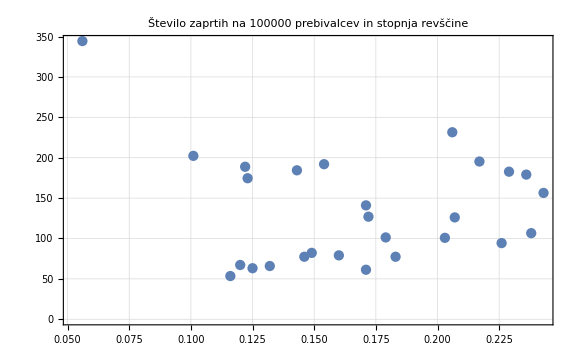

```mathematica
ListPlot[RegresijskaPremicaPodatki3,LabelingFunction->Tooltip,PlotLabel->"Število zaprtih na 100000 prebivalcev in stopnja revščine",PlotTheme->"Detailed",ImageSize->Large]
```

```mathematica
PodatkiRevscinaZaprti =Normal[RegresijskaPremicaPodatki2[All,{If[#Country=="Czech Republic",QuantityMagnitude[Entity["Country","CzechRepublic"][EntityProperty["Country","PovertyHeadcount",{"Date"->2018}]]]/100,QuantityMagnitude[Entity["Country",#Country][EntityProperty["Country","PovertyHeadcount",{"Date"->2018}]]]/100],#[[2]]}&]]
```

{{0.056,344.4},{0.226,94.3},{0.101,202.3},{0.123,174.6},{0.154,192.},{0.238,106.6},{0.122,188.8},{0.125,63.2},{0.217,195.3},{0.116,53.5},{0.149,82.2},{0.229,182.7},{0.206,231.5},{0.171,61.3},{0.143,184.4},{0.183,77.4},{0.179,101.3},{0.203,100.8},{0.171,141.},{0.236,179.1},{0.172,127.},{0.243,156.4},{0.12,67.2},{0.207,126.1},{0.16,79.1},{0.132,65.9},{0.146,77.4}}

Poiščemo regresijsko premico:

```mathematica
regresijskaPremica=LinearModelFit[PodatkiRevscinaZaprti,x,x]
```

FittedModel[167.936-194.007 x]

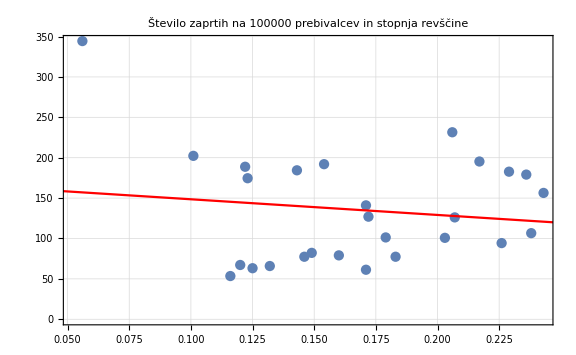

```mathematica
Show[ListPlot[RegresijskaPremicaPodatki3,LabelingFunction->Tooltip,PlotLabel->"Število zaprtih na 100000 prebivalcev in stopnja revščine",PlotTheme->"Detailed",ImageSize->Large],
Plot[regresijskaPremica["BestFit"],{x,0,0.3},PlotStyle->{Red}]]
```

Regresijska premica, nam za dane podatke ne kaže, da bi revščina imela kakršenkoli vpliv na število zapornikov. Zaradi velikega odstopanja Belorusije, ki ima eno izmed najnižjih stopenj revščine v Evropi, a veliko zapornikov s pomočjo regresijske premice ne moremo razbrati vpliva.

```mathematica
DSV3=Dataset[ZenskeZaporiBrezUK2011][All,List[Which[#COUNTRY=="Czechia",Entity["Country","CzechRepublic"],#COUNTRY=="Germany (until 1990 former territory of the FRG)",Entity["Country","Germany"],#COUNTRY=="Kosovo (under United Nations Security Council Resolution 1244/99)",Entity["Country","Kosovo"],#COUNTRY=="Bosnia and Herzegovina",Entity["Country","Bosnia"],#COUNTRY=="North Macedonia",Entity["Country","Macedonia"],!MemberQ[{"Czechia","Germany (until 1990 former territory of the FRG)","Kosovo (under United Nations Security Council Resolution 1244/99)"},#COUNTRY],Entity["Country",#COUNTRY]]-> #[[2]]]&];
```

```mathematica
PodatkiDrzava[drzava_]:=Module[{DrzavaPodatki,DrzavaAbsolutno,DrzavaAbsolutnoTimeSeries},
DrzavaPodatki = evropskeDrzaveZaporniki[Select[#Country==drzava["Name"]&]];
DrzavaAbsolutno = DrzavaPodatki[All, Join[{3},Range[5,36, 2]]][All,Range[2,17]]//Normal//Values;
DrzavaAbsolutnoTimeSeries=TimeSeries[DrzavaAbsolutno[[1]],{Range[2003,2018]}];
GeoListPlot[drzava,GeoRange->Quantity[500,"Miles"],ImageSize->Medium]
ListLinePlot[DrzavaAbsolutnoTimeSeries,ImageSize->Large,PlotTheme->"Detailed",Frame->False,Axes->True,AxesLabel->{"Year","Rate"},PlotLegends->{drzava["Name"]},PlotMarkers->{"●"},PlotLabel->Style[StringForm[ToUpperCase[drzava["Name"]], "(absolute values)"],Large,Darker[Red]]]
];
```

```mathematica
Obrazec = FormPage["Drzava"->Drzave2Entitete,PodatkiDrzava[#Drzava]&,AppearanceRules-><|"Title"->"Podatki o številu zaprtih oseb","Description"->"Vnesi ime države, za katero želiš prikazati podatke.","SubmitLabel"->"Prikazi"|>]
```

```mathematica
CloudDeploy[Obrazec,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/404719e1-d24f-4530-95e1-bb68325fdeb6]